# Cost of Dai Collateral Attack

```mathematica
LiquidationThreshold = 1.5;
DaiCirculation =77000000;
EthCollateral = 355000000;
KeeperDiscount = 0.03;
AvgTxPrice = 0.20;
CDPOpenNumTx =1;
CDPClosingNumTx = 6;
PETHEx = 1.04;
```

## Decrease overall collateral ratio (simple)

```mathematica
collateral[target_, CDPratio_] = (EthCollateral - target * DaiCirculation) / (target - CDPratio);
```

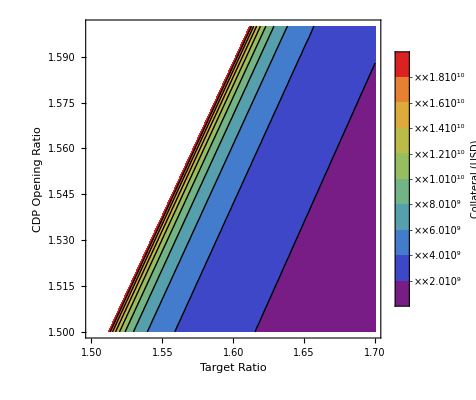

```mathematica
min = 0;
max = 2*10^10;
ContourPlot[collateral[t,r],{t,1.5,1.7}, {r,1.5,1.6},FrameLabel->{"Target Ratio", "CDP Opening Ratio"}, PlotLegends-> BarLegend[Automatic, LegendLabel->"Collateral (USD)"], PlotRange->{min,max}, PlotTheme->"Scientific",ColorFunctionScaling->False, ColorFunction->(ColorData["Rainbow"][Rescale[#,{min,max}]]&), Contours->9, ScalingFunctions->{None,None,None}]
```

## Decrease overall collateral ratio (including tx cost)